## Depth prediction models from the reference horizon

### Input sets of horizons

```mathematica
set1= {1, {2,1}, {2,1}, {3,3}, {3,3}};
set2= {3, {4,1}, {4,2}, {5,3}, {5,4}};(*{reference h., {predicted h., method},..., {predicted h., method}}*)

(*also you need : wellDataset, reference horizons and time sections (isochrons)! use test.nb from PARAMETRES to WELLS*)
```

### Evaluation

```mathematica
Print["*****************************dHdT*********************************"]
(*!!!!!!!!!!! horizons - here paste set of horizons from which reference horizon must be selected*)
dlmSetHT1= AllMethods[set1, horizons,  wellDataset, time, dt, dh][["lmSetHT"]]
dlmParametresHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresHT"]];
dresultHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultHT"]];
dplotDataHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataHT"]];

dlmSetHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetHT"]]
dlmParametresHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresHT"]];
dresultHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultHT"]];
dplotDataHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataHT"]];

Print["*****************************dVdT*********************************"]

dlmSetVT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmSetVT"]]
dlmParametresVT1=AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresVT"]];
dresultVT1=AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultVT"]];
dplotDataVT1 = AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataVT"]];

dlmSetVT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetVT"]]
dlmParametresVT2=AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresVT"]];
dresultVT2=AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultVT"]];
dplotDataVT2 = AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataVT"]];

Print["*****************************dTdH*********************************"]

dlmSetTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmSetTH"]]
dlmParametresTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresTH"]];
dresultTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultTH"]];
dplotDataTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataTH"]];

dlmSetTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetTH"]]
dlmParametresTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresTH"]];
dresultTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultTH"]];
dplotDataTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataTH"]];


Print["*****************************dVave*********************************"]

dresultVave1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultVave"]];
dvAveTable1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["vAveTable"]]

dresultVave2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultVave"]];
dvAveTable2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["vAveTable"]]
```

*****************************dHdT*********************************

{FittedModel[-1.25465+2897.3 dt],FittedModel[-1.25465+2897.3 dt]}

{FittedModel[-458.079+7917.5 dt]}

*****************************dVdT*********************************

{}

{FittedModel[14.6692-141.673 dt]}

*****************************dTdH*********************************

{FittedModel[0.00199783+0.000266753 dh],FittedModel[0.00199783+0.000266753 dh]}

{FittedModel[-0.0690686+0.000290212 dh]}

*****************************dVave*********************************

{}

{4186.05}

### Linear regression plots for set1

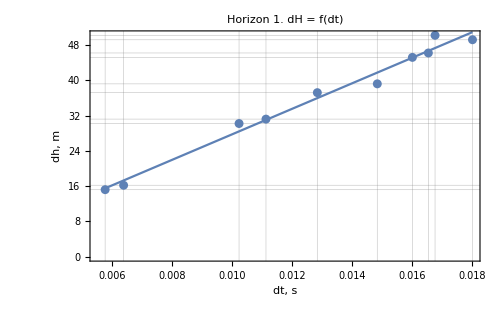
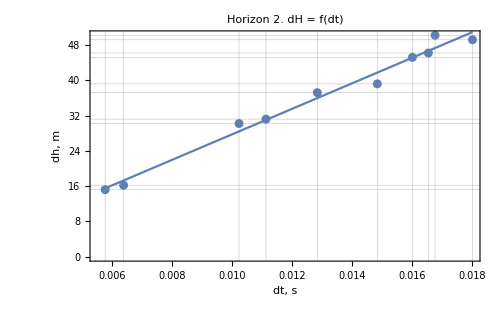

{}

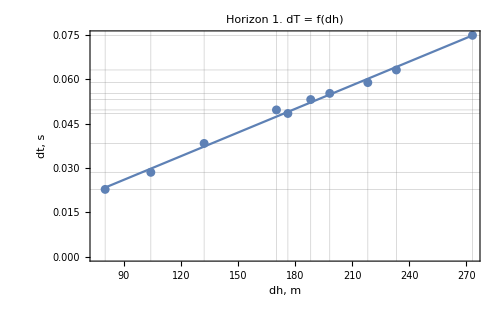
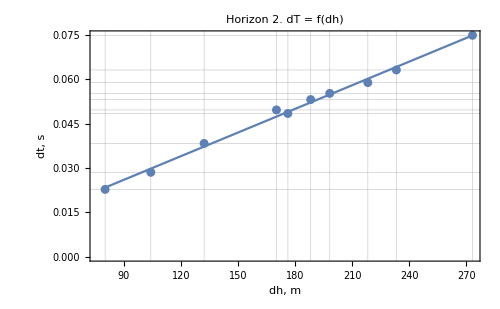

```mathematica
LinearRegressionPlots[dplotDataHT1,dlmSetHT1, dt, "dH = f(dt)", {"dt, s","dh, m"}]
LinearRegressionPlots[dplotDataVT1[[All, All,2;;3]],dlmSetVT1, dt, "dV = f(dt)", {"dt, s","dv, m/s"}]
LinearRegressionPlots[dplotDataTH1,dlmSetTH1, dh, "dT = f(dh)", {"dh, m","dt, s"}]
```

### Linear regression plots for set2

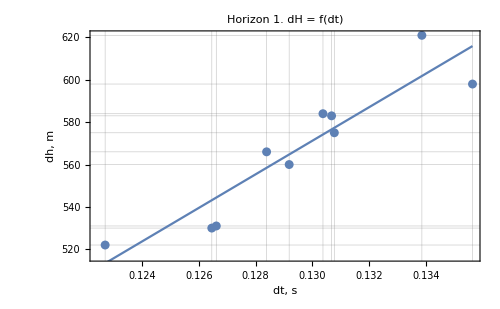

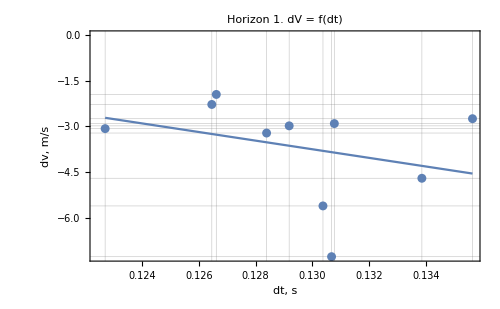

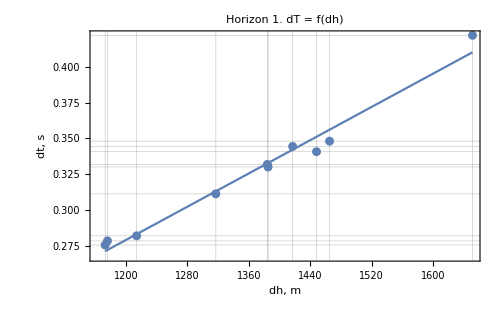

```mathematica
LinearRegressionPlots[dplotDataHT2,dlmSetHT2, dt, "dH = f(dt)", {"dt, s","dh, m"}]
LinearRegressionPlots[dplotDataVT2[[All, All,2;;3]],dlmSetVT2, dt, "dV = f(dt)", {"dt, s","dv, m/s"}]
LinearRegressionPlots[dplotDataTH2,dlmSetTH2, dh, "dT = f(dh)", {"dh, m","dt, s"}]
```

## Results for set1

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[dresultHT1, PlotStyle->{Pink}],
	ListLinePlot[dresultVT1 , PlotStyle->{Purple}],
	ListLinePlot[dresultTH1, PlotStyle->{Orange}],
ListLinePlot[dresultVave1, PlotStyle->{Brown}]
]
```

-Graphics-

### Results for set2

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[dresultHT2, PlotStyle->{Pink}, PlotLegends->{"dH = f(dt)"}],
	ListLinePlot[dresultVT2 , PlotStyle->{Purple}, PlotLegends->{"dV = f(dt)"}],
	ListLinePlot[dresultTH2, PlotStyle->{Orange}, PlotLegends->{"dT = f(dh)"}],
ListLinePlot[dresultVave2, PlotStyle->{Brown}, PlotLegends->{"dVave"}]

]
```

-Graphics-